New version of the autoamplitude program based on the exact matrix elements Miguel included in the longer analytical paper.

Generating function used to define the physical states - we need to check these against the solutions we had before just to make sure....

```mathematica
FId[x_]:=-2(Log[1+x]+Log[Gamma[1/2+ⅈ Log[x]/(2π)]])
```

The following are the generating functions used to obtain the matrix elements of $\sqrt {\Theta}/(\sqrt {12\pi G}), the identity operators, and the evolution operator respectively.

```mathematica
ThK[n_,m_]:= -Sqrt[n*m](n+m)/2;
ThD[n_]:=2 n^2
Aexact[n_,m_]:= 2 Sqrt[n*m] SeriesCoefficient[FId[ⅇ^x(1+s)/(1-s)(1-t)/(1+t)],{s,0,2n},{t,0,2m}];
```

The following are the definitions required for the algorithm to function.  Degen and w together identify the number of distinct volumes taken along the path and count the degeneracy of the values.

```mathematica
degen[v_]:=Table[Length[Split[Sort[v]][[i]]],{i,1,Length[Split[Sort[v]]]}];
w[v_]:=Table[Split[Sort[v]][[i]][[1]],{i,1,Length[Split[Sort[v]]]}];
c[w_]:=Table[ThD[w[[i]]],{i,1,Length[w]}];
```

The following produces the diagonal matrix elements corresponding to the distinct values of volume.

Note that if we take x in the following equations to be Sqrt[12 π G] then we are not missing any factors and the result is exact.
Simply need to call Amplitude with the full history in volume.

```mathematica
IPartBase[w_,deg_]:=Product[1/((deg[[i]]-1)!),{i,1,Length[w]}]Sum[ⅇ^(ⅈ*Sqrt[d[[i]]]*x)Product[1/(d[[i]]-d[[j]]),{j,1,i-1}]* Product[1/(d[[i]]-d[[j]]),{j,i+1,Length[w]}],{i,1,Length[w]}];
IPartDer[w_,deg_]:=Fold[D[#1,#2]&,IPartBase[w,deg],Table[{d[[i]],deg[[i]]-1},{i,1,Length[w]}]];
IPart[w_,deg_,c_]:=Evaluate[IPartDer[w,deg]]/.d->c
ProdPart[v_]:=Product[ThK[v[[i]],v[[i+1]]],{i,1,Length[v]-1}];
Amplitude[v_]:=( wv=w[v]; deg=degen[v]; diagl=c[wv];  ProdPart[v]*IPart[wv, deg, diagl]);
```

Tools for generating sets of paths!

Changes generates a set of possible changes between two equal volumes but only over single steps
Paths then generates the actual sets of paths here starting from volume = 4
NullPath checks to see if that path passes through zero
ManyAmp then computes the amplitude for a whole set of paths

```mathematica
Changes[m_,vi_,vf_]:=(
diff=(vf-vi);
base=Join[Table[1,{i,1,m/2+diff/2}],Table[-1,{i,1,m/2-diff/2}]];
changes=Permutations[base];
numpaths=Length[changes];
 initial = vi;)
    
Paths[changes_]:=(
numpaths=Length[changes];
m=Length[changes[[1]]];
paths=Table[1,{j,1,numpaths}];
path=Table[initial,{i,1,m+1}];
k=1;
For[j=1,j≤numpaths,j++,
valid=1;
For[i=1,i≤m,i++,
path[[i+1]]=path[[i]]+changes[[j]][[i]];
If[path[[i+1]]<1,valid=0];];
If[valid==1,
paths[[k]]=path;
k++;];
];
numpaths=k-1;);
ManyAmp[m_,vi_,vf_]:=(
Changes[m,vi,vf];
Paths[changes];
Many=0;
For[i=1,i≤numpaths,i++,
Many=Many+Amplitude[paths[[i]]]];
;
Many)
```

```mathematica
Changes[4,1,3]
changes
Paths[4,1,3]
paths
```

{{1,1,1,-1},{1,1,-1,1},{1,-1,1,1},{-1,1,1,1}}

{{1,2,3,4,3},{1,2,3,2,3},{1,2,1,2,3},{1,0,1,2,3}}

Below here is all testing the amplitude!!

```mathematica
ManyAmp[1,1,2]
```

-(3 (-1/6 ⅇ^(ⅈ √2 x)+1/6 ⅇ^(2 ⅈ √2 x)))/(√2)

ⅇ^(ⅈ √2 x)

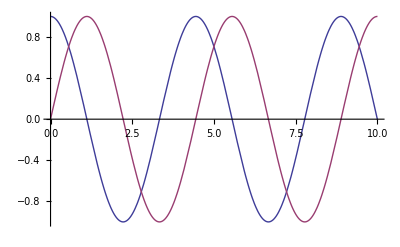

```mathematica
Amp0 = ManyAmp[0,1,1]
Plot[{Re[Amp0],Im[Amp0]},{x,0,10}]
```

9/2 (-1/36 ⅇ^(ⅈ √2 x)+1/36 ⅇ^(2 ⅈ √2 x)-(ⅈ ⅇ^(ⅈ √2 x) x)/(12 √2))

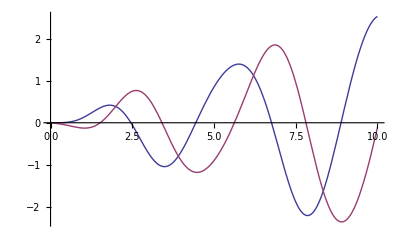

```mathematica
Amp2=ManyAmp[2,1,1]
Plot[{Re[Amp2],Im[Amp2]},{x,0,10}]
```

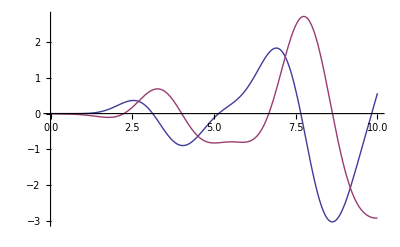

```mathematica
Amp3=ManyAmp[4,1,1];
Plot[{Re[Amp3],Im[Amp3]},{x,0,10}]
```

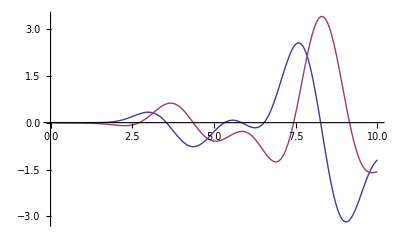

```mathematica
Amp4=ManyAmp[6,1,1];
Plot[{Re[Amp4],Im[Amp4]},{x,0,10}]
```

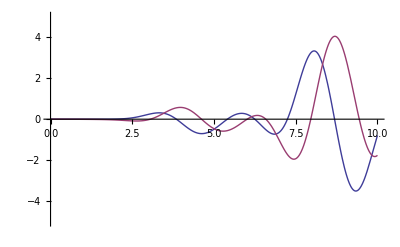

```mathematica
Changes[8];
Paths[8];
ManyAmp[paths];
Amp5=Many;
Plot[{Re[Amp5],Im[Amp5]},{x,0,10},PlotRange->{-5,5}]
```

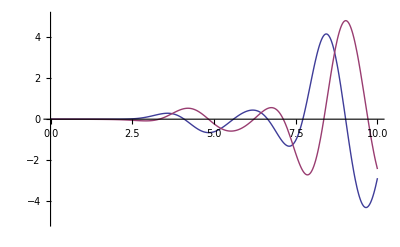

```mathematica
Changes[10];
Paths[10];
ManyAmp[paths];
Amp6=Many;
Plot[{Re[Amp6],Im[Amp6]},{x,0,10},PlotRange->{-5,5}]
```

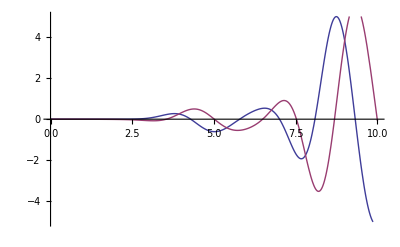

```mathematica
Changes[12];
Paths[12];
ManyAmp[paths];
Amp7=Many;
Plot[{Re[Amp7],Im[Amp7]},{x,0,10},PlotRange->{-5,5}]
```

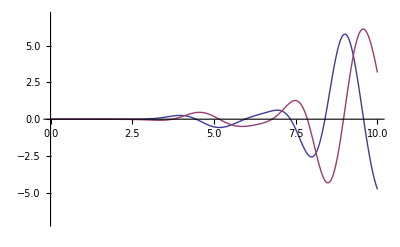

```mathematica
Changes[14];
Paths[14];
ManyAmp[paths];
Amp8=Many;
Plot[{Re[Amp8],Im[Amp8]},{x,0,10},PlotRange->{-7,7}]
```

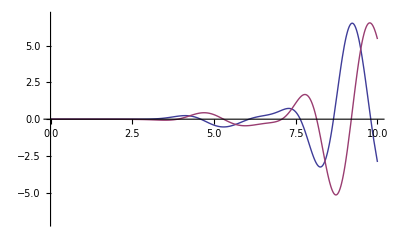

```mathematica
Changes[16];
Paths[16];
ManyAmp[paths];
Amp9=Many;
Plot[{Re[Amp9],Im[Amp9]},{x,0,10},PlotRange->{-7,7}]
```

```mathematica
Amp=0;
For[m=0,m≤18,m=m+2,
Changes[m];
Paths[m];
ManyAmp[paths];
Amp=Amp+Many;];
```

$Aborted

```mathematica
aex = Aexact[1,1];
```

```mathematica
Amp=Amp0+Amp2+Amp3+Amp4+Amp5+Amp6+Amp7+Amp8+Amp9;
```

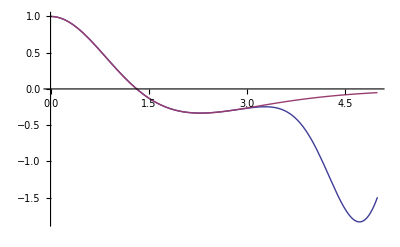

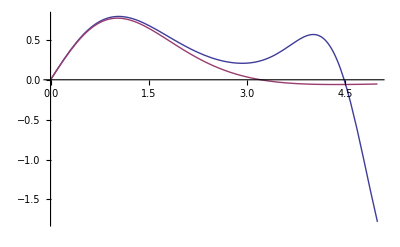

```mathematica
Plot[{Re[Amp],Re[aex]},{x,0,5}]
Plot[{Im[Amp],Im[aex]},{x,0,5}]
```

Problem with this system!! Either with the calculations here or with the real model ?? hmmm~ check if the exact solution does solve the constraint!! And then check the if the automated calculation is working correclty outside of the simple model.

```mathematica
aex2=Aexact[3,1];
```

```mathematica
aapprox=ManyAmp[2,1,3]
```

15/2 √3 (1/96 ⅇ^(ⅈ √2 x)-1/60 ⅇ^(2 ⅈ √2 x)+1/160 ⅇ^(3 ⅈ √2 x))

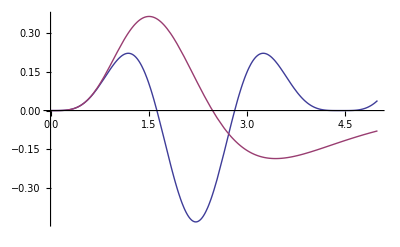

```mathematica
Plot[{Re[aapprox],Re[aex2]},{x,0,5}]
```

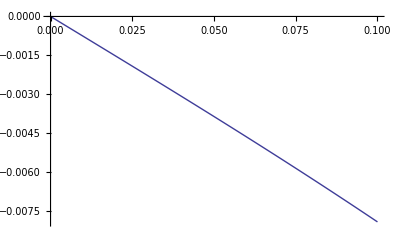

```mathematica
Plot[{Im[15/2 √3 (+1/96 ⅇ^(ⅈ √2 x)-1/60 ⅇ^(2 ⅈ √2 x)+1/160 ⅇ^(3 ⅈ √2 x))],Im[aex2]},{x,0,0.1}]
```